```mathematica
BeginPackage["PlotPath`"];
getVariables;
multiDimComposition;
makeFunction;
variableList;
arcLength;
paramPath;
plotPath;

Begin["`Private`"];

Clear[getVariables]
SetAttributes[getVariables,HoldFirst];
getVariables[expr_,f_:Identity,Optional[excludedContexts:{__String},{"System`"}]]:=Cases[Unevaluated[expr],a_Symbol/;!(MemberQ[excludedContexts,Context[a]]||MemberQ[Attributes[a],Locked|ReadProtected]):>f[a],{0,Infinity}]//DeleteDuplicates

Clear[multiDimComposition]
multiDimComposition[flst__]:=With[{fcns=Reverse@List[flst]},Fold[#2[Sequence@@#1]&,First[fcns][##],Rest[fcns]]&]

Clear[makeFunction];
SetAttributes[makeFunction,HoldAll];

(*This first form allows pure functions to be used*)
makeFunction[afcn_Function,_.]:=afcn
makeFunction[fexpr_]:=makeFunction[fexpr,Automatic]
makeFunction[fexpr_,vars:{__Symbol}|Automatic]:=Module[{ivars=Hold[vars]},ivars=If[ivars===Hold[Automatic],(*GetVariables returns {Hold[x_]..} we want Hold[{x_..}]*)Distribute[Sort[getVariables[fexpr,Hold]],Hold],ivars];
Function@@Join[ivars,Hold[fexpr]]]


Clear[plotPath];
Options[plotPath]=Options[Plot];

plotPath[fcn:Except[_List],args__]:=plotPath[{fcn},args]
plotPath[fcns_List,params_,{s_Symbol,smin_,smax_},opts:OptionsPattern[]]:=With[{pfcn=makeFunction[params],fcnlst=makeFunction/@fcns},Plot@@{multiDimComposition[#,pfcn][s]&/@fcnlst,{s,smin,smax},FilterRules[{opts},Options[Plot]]}]


Clear[arcLength];
arcLength[p1_List,p2_List]/;(Length[p1]==Length[p2]):=Norm[p2-p1]
arcLength[p:{_List..}]/;Check[Transpose[p];True,False]:=Plus@@arcLength@@@Partition[p,2,1]

Clear[paramPath]
paramPath[p1_List,p2_List][s_]/;(Length[p1]≥2&&Length[p2]≥2&&Length[p1]==Length[p2]):=p1+s (p2-p1)/Norm[p2-p1]


paramPath[p:{_List..}][s_]/;Check[Transpose[p];True,False]:=Block[{ptpairs=Partition[p,2,1],conds,paths,dists},dists={0}~Join~Accumulate[arcLength@@@ptpairs];
conds=dists//Partition[#,2,1]&;
paths=paramPath[Sequence@@#[[1]]][s-#[[2]]]&/@Thread[List[ptpairs,Most[dists]]]//Transpose;
(*This creates seperate Piecewise functions,one for the x,y,etc.coords,respectively.*)Piecewise[{#[[1]],#[[2,1]]≤s≤#[[2,2]]}&/@Thread[List[#,conds]]]&/@paths]


(*Accepts lists of points*)
plotPath[fcn_,pts_List,opts:OptionsPattern[]]:=Module[{s},plotPath[fcn,paramPath[pts][s],{s,0,arcLength[pts]},opts]]

(*Accepts points plus labels*)
plotPath[fcn_,pts:{{_List,_String}..},opts:OptionsPattern[]]:=Module[{s,xticks,rls,ticks,xgrid,grid,tname},(*generate tick marks/gridlines for the labels*)xgrid={0}~Join~Accumulate[arcLength@@@Partition[pts[[All,1]],2,1]];
xticks=Thread[{xgrid,pts[[All,2]]}];
(*Substitute in tick and grid specifications*)tname=If[OptionValue[Frame],FrameTicks,Ticks];
ticks=OptionValue[tname];
ticks=tname->Which[ticks===None (*Don't override this one only*),None,ticks===Automatic,{xticks,Automatic},True,MapAt[#/.Automatic->xticks&,ticks,If[OptionValue[Frame],2,1]]];
grid=GridLines->If[OptionValue[GridLines]===Automatic||OptionValue[GridLines]===None,{xgrid,None},MapAt[#/.Automatic->xgrid&,OptionValue[GridLines],1]];
rls={ticks,grid,FilterRules[List@opts,Except[{Ticks,FrameTicks}]]};
plotPath[fcn,Evaluate[pts[[All,1]]],Evaluate[rls]]]
End[(*`Private`*)];
EndPackage[(*PlotPath*)];
```

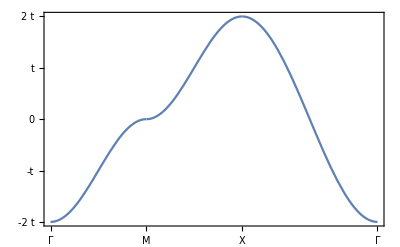

```mathematica
plotPath[-2 (Cos[π kx]+Cos[π ky]),{{{0,0},"Γ"},{{1,0},"M"},{{1,1},"X"},{{0,0},"Γ"}},Frame->True,FrameTicks->{{#,#}&@Thread[{Range[-4,4,2],Range[-2,2] "t"}],{Automatic,Automatic}}]
```

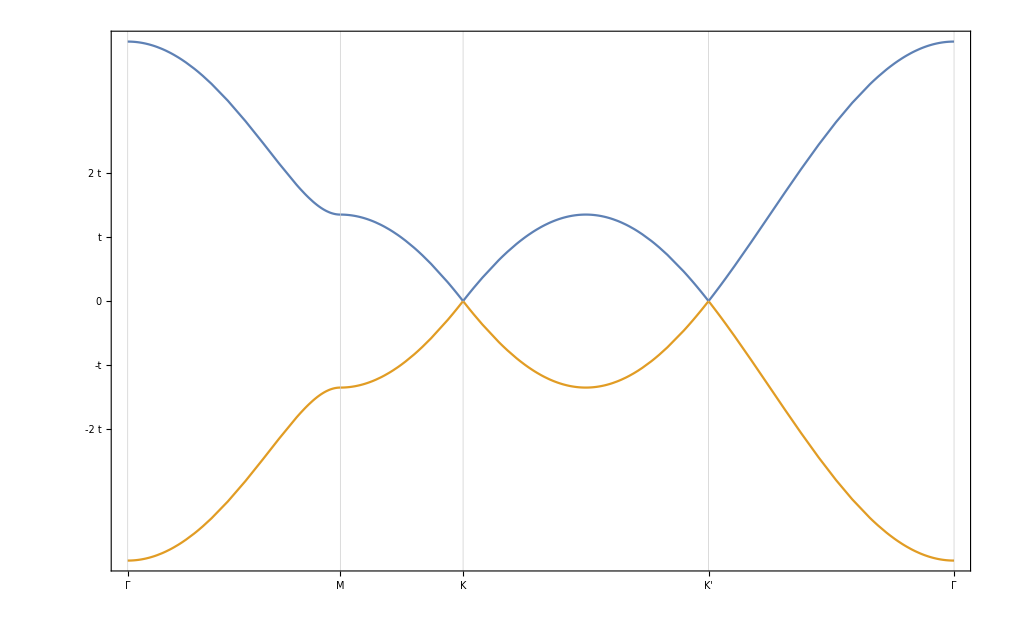

```mathematica
a = 1.42;
a1 = a/2{3,√3 }; a2 = a/2{3,-√3 };
δ1 = a  {-1, 0}; δ2 = δ1 + a1; δ3 = δ1+a2;
b1 = (2 Pi)/3 {1, √3}; b2 = (2 Pi)/3 {1 , -√3};

K = {(2 Pi)/(3 a), (2 Pi)/(3 a √3)}; K' = {(2 Pi)/(3 a), -(2 Pi)/(3 a √3)};
M = {K[[1]],0};

f[kx_, ky_] := 2.7  √(3 + 2 Cos[√3 ky  a] + 4 Cos[(√3)/2 ky a] Cos[3/2 kx a]);

plotPath[{f[kx,ky], -f[kx,ky]},{{{0,0},"Γ"},{M,"M"},{K,"K"}, {K', "K'"},{{0,0},"Γ"}},ColorFunction->Black,  Frame->True,FrameTicks->{{#,#}&@Thread[{Range[-4,4,2],Range[-2,2] "t"}],{Automatic,Automatic}}]
```